# DPC Light

Using the simple xls file

```mathematica
dat=Import["/Users/jeanpierretollenboom/Desktop/DPC Light.xlsx",{"Sheets",1}]
```

{{,,,,,},{Task,weight,Accumulated,Due time index,Actual time completed,Progress},{A,10.,10.,2.,3.,4.},{B,20.,30.,2.,3.,9.},{C,50.,80.,4.,5.,25.},{D,50.,130.,6.,7.,40.},{E,100.,230.,8.,10.,71.},{F,20.,250.,10.,12.,77.},{G,20.,270.,12.,13.,83.},{H,20.,290.,16.,17.,89.},{I,20.,310.,20.,22.,95.},{J,5.,315.,22.,23.,97.},{K,10.,325.,24.,24.,100.}}

```mathematica
dat=Drop[dat,2]
```

{{A,10.,10.,2.,3.,4.},{B,20.,30.,2.,3.,9.},{C,50.,80.,4.,5.,25.},{D,50.,130.,6.,7.,40.},{E,100.,230.,8.,10.,71.},{F,20.,250.,10.,12.,77.},{G,20.,270.,12.,13.,83.},{H,20.,290.,16.,17.,89.},{I,20.,310.,20.,22.,95.},{J,5.,315.,22.,23.,97.},{K,10.,325.,24.,24.,100.}}

```mathematica
bluepts=Transpose[{dat[[All,4]],dat[[All,6]]}]
```

{{2.,4.},{2.,9.},{4.,25.},{6.,40.},{8.,71.},{10.,77.},{12.,83.},{16.,89.},{20.,95.},{22.,97.},{24.,100.}}

```mathematica
blackpts=Transpose[{dat[[All,5]],dat[[All,6]]}]
```

{{3.,4.},{3.,9.},{5.,25.},{7.,40.},{10.,71.},{12.,77.},{13.,83.},{17.,89.},{22.,95.},{23.,97.},{24.,100.}}

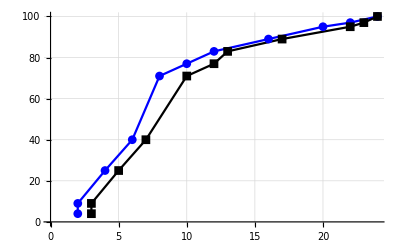

```mathematica
ListLinePlot[
{bluepts,blackpts},PlotStyle->{Blue,Black},GridLines->Automatic,PlotMarkers->Automatic]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Desktop","pic.png"}],%]
```

/Users/jeanpierretollenboom/Desktop/pic.png